## MoS2: June 2018

```mathematica
data=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/June14_2018_test12 MoS2.csv","CSV"];
```

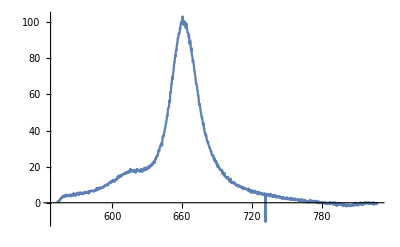

```mathematica
ListLinePlot[data⟦2;;-1⟧,PlotRange->All]
```

```mathematica
data⟦-1⟧
```

{827.964,-0.7}

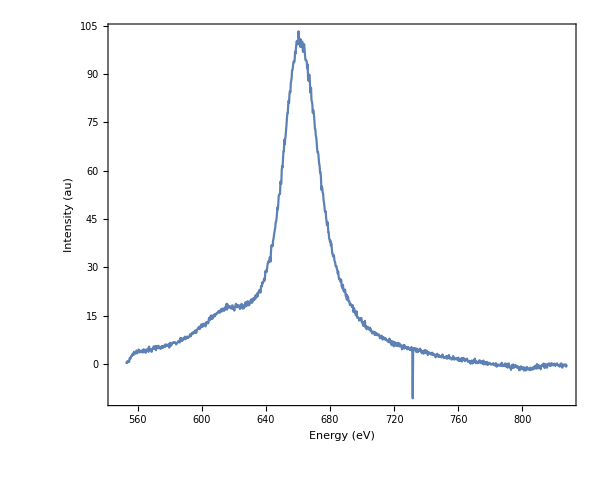

```mathematica
ListLinePlot[data⟦2;;-1⟧,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
data⟦667⟧
```

{731.637,-10.6}

```mathematica
data = Delete[data,667];
```

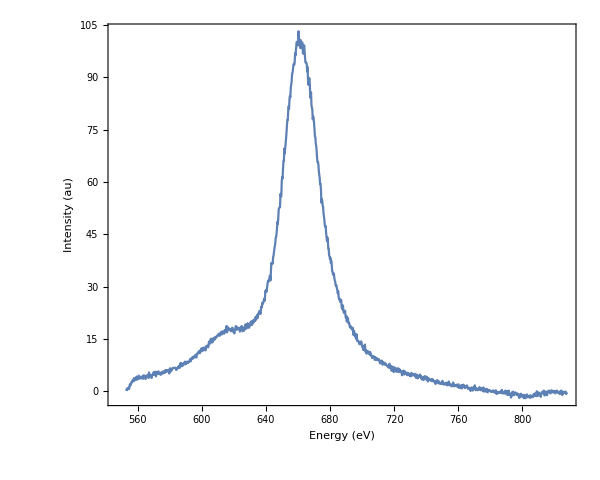

```mathematica
ListLinePlot[data⟦2;;-1⟧,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
evData=Table[{1239.8/data⟦i+1,1⟧,data⟦i+1,2⟧},{i,Length[data]-1}];
```

```mathematica
fit=Interpolation[evData⟦2;;-1⟧,InterpolationOrder->1];
```

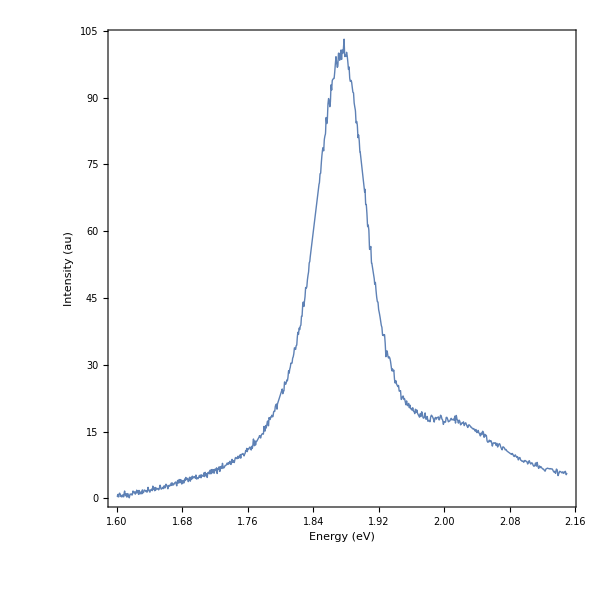

```mathematica
Plot[fit[x],{x,1.6,2.15},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->Thick]
```

## Attempting a Gaussian peak fit:

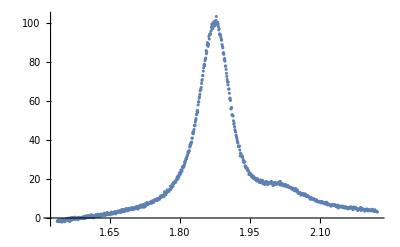

```mathematica
peak=evData⟦20;;-80⟧;
ListPlot[peak, PlotRange->All]
```

```mathematica
ClearAll[gaussmodel]
gaussmodel[height_,width_,position_]:=height Exp[-(x-position)^2/(2 width^2)]
```

```mathematica
nlm=NonlinearModelFit[peak,
Sum[gaussmodel[height[i],width[i],position[i]],{i,2}],
{{height[1],80},{width[1],0.1},{position[1],1.86},
{height[2],10},{width[2],0.2},{position[2],2.0},
{height[3],10},{width[3],0.1},{position[3],1.88}
},x];

nlm["BestFitParameters"]
```

{height[1]→78.1872,width[1]→0.0299759,position[1]→1.87262,height[2]→21.5555,width[2]→0.134801,position[2]→1.91747,height[3]→10.,width[3]→0.1,position[3]→1.88}

```mathematica
(nlm["CorrelationMatrix"]/. v_:>Style[v,Red]/;0.7≤Abs[v]<1)//MatrixForm
```

(1. | 0.05106 | 0.0720749 | -0.588249 | 0.453843 | 0.359407 | Indeterminate | Indeterminate | Indeterminate
0.05106 | 1. | 0.0928039 | -0.646726 | 0.425738 | 0.376921 | Indeterminate | Indeterminate | Indeterminate
0.0720749 | 0.0928039 | 1. | -0.172112 | 0.194543 | -0.140604 | Indeterminate | Indeterminate | Indeterminate
-0.588249 | -0.646726 | -0.172112 | 1. | -0.759022 | -0.421141 | Indeterminate | Indeterminate | Indeterminate
0.453843 | 0.425738 | 0.194543 | -0.759022 | 1. | 0.383349 | Indeterminate | Indeterminate | Indeterminate
0.359407 | 0.376921 | -0.140604 | -0.421141 | 0.383349 | 1. | Indeterminate | Indeterminate | Indeterminate
Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate)

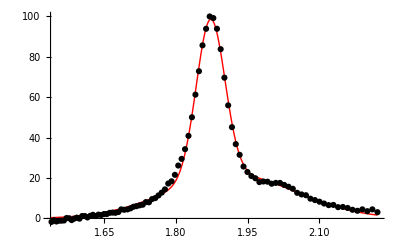

```mathematica
Show[
  Plot[
    nlm[x], Evaluate@Flatten@{x, MinMax@peak⟦All, 1⟧},
    PlotStyle -> Directive[Thick, Red], PlotRange->All
  ],
  ListPlot[peak[[;; ;; 10]], PlotStyle -> Black]
]
```

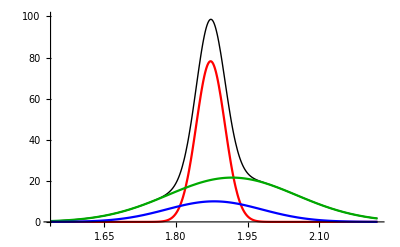

```mathematica
Show[(*fitted peak-baseline*)Plot[nlm[x]/. nlm["BestFitParameters"],Evaluate@Flatten@{x,MinMax@peak[[All,1]]},PlotStyle->Directive[Thick,Black],PlotRange->{0,100}],(*single components*) MapThread[Plot[#1,Evaluate@Flatten@{x,MinMax@peak[[All,1]]},PlotStyle->#2,PlotRange->All]&,{Table[gaussmodel[height[i],width[i],position[i]]/. nlm["BestFitParameters"],{i,3}],{Red,Darker@Green,Blue}}]]
```

## WS2: Feb 2018

```mathematica
dataMonolayer=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/spectrum06.csv","CSV"];
```

```mathematica
evDataMono=Table[{1239.8/dataMonolayer⟦i+1,1⟧,dataMonolayer⟦i+1,2⟧},{i,Length[dataMonolayer]-1}];
```

```mathematica
fitMono=Interpolation[evDataMono⟦2;;-1⟧,InterpolationOrder->1];
```

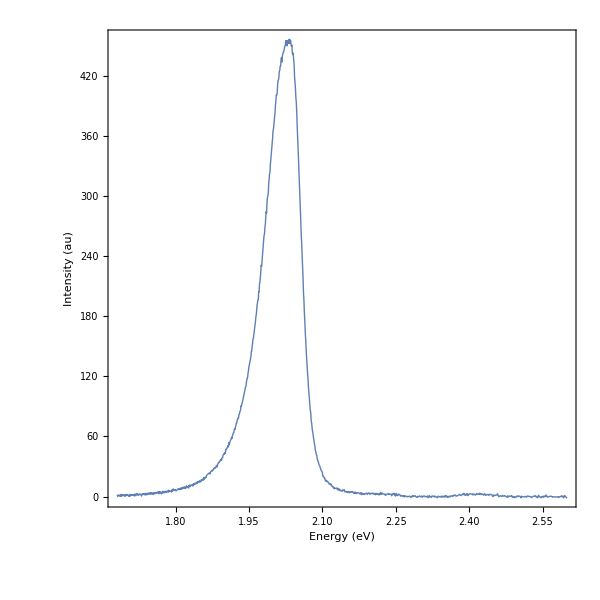

```mathematica
Plot[fitMono[x],{x,1.68,2.6},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->Thick]
```

```mathematica
Quiet@FindMaximum[fitMono[x],{x,2.0}]
```

{455.7,{x→2.0349}}

```mathematica
dataBilayer=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/spectrum05_bi.csv","CSV"];
```

```mathematica
evDataBi=Table[{1239.8/dataBilayer⟦i+1,1⟧,dataBilayer⟦i+1,2⟧},{i,Length[dataBilayer]-1}];
```

```mathematica
fitBi=Interpolation[evDataBi⟦2;;-1⟧,InterpolationOrder->1];
```

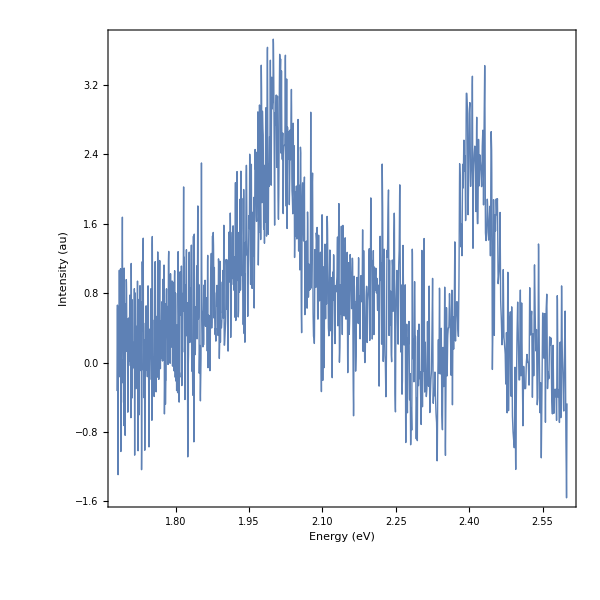

```mathematica
Plot[fitBi[x],{x,1.68,2.6},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->Thick]
```

```mathematica
dataMultilayer=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/spectrum07_layers.csv","CSV"];
```

```mathematica
evDataMulti=Table[{1239.8/dataMultilayer⟦i+1,1⟧,dataMultilayer⟦i+1,2⟧},{i,Length[dataMultilayer]-1}];
```

```mathematica
fitMulti=Interpolation[evDataMulti⟦2;;-1⟧,InterpolationOrder->1];
```

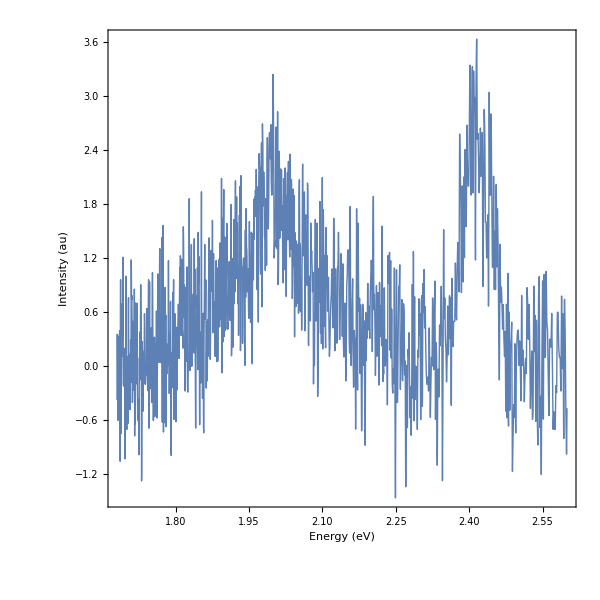

```mathematica
Plot[fitMulti[x],{x,1.68,2.6},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->Thick]
```

Combine

```mathematica
Quiet@FindMaximum[fitMono[x],{x,2}]
```

{455.7,{x→2.0349}}

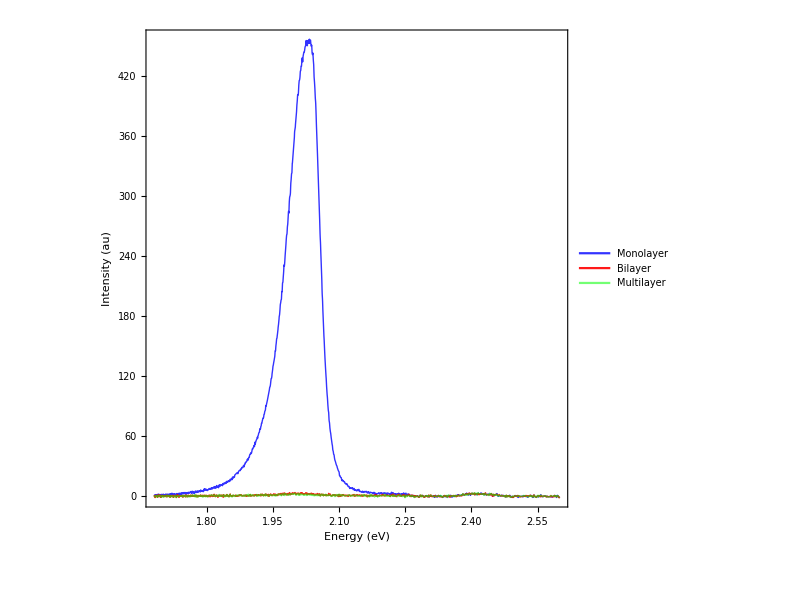

```mathematica
Plot[{fitMono[x],fitBi[x],fitMulti[x]},{x,1.68,2.6},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->{{Blue,Thick,Opacity[0.8]},{Red,Thick,Opacity[0.9]},{Green,Thick,Opacity[0.55]}},PlotLegends->Placed[{"Monolayer","Bilayer","Multilayer"},{Right,Top}]]
```

## MoS2: Oct 2017

```mathematica
spot23=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/MoS2_23.csv","CSV"];
```

```mathematica
spot24=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/MoS2_24.csv","CSV"];
```

```mathematica
spot25=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/MoS2_25.csv","CSV"];
```

```mathematica
spot26=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/MoS2_26.csv","CSV"];
```

```mathematica
rescaledIntensity23=Rescale[spot23⟦2;;-1,2⟧];
rescaledIntensity24=Rescale[spot24⟦2;;-1,2⟧];
rescaledIntensity25=Rescale[spot25⟦2;;-1,2⟧];
rescaledIntensity26=Rescale[spot26⟦2;;-1,2⟧];
```

```mathematica
evSpot23=Table[{1239.8/spot23⟦i+1,1⟧,rescaledIntensity23⟦i⟧},{i,Length@spot23-1}];
evSpot24=Table[{1239.8/spot24⟦i+1,1⟧,rescaledIntensity24⟦i⟧},{i,Length@spot24-1}];
evSpot25=Table[{1239.8/spot25⟦i+1,1⟧,rescaledIntensity25⟦i⟧},{i,Length@spot25-1}];
evSpot26=Table[{1239.8/spot26⟦i+1,1⟧,rescaledIntensity26⟦i⟧},{i,Length@spot26-1}];
```

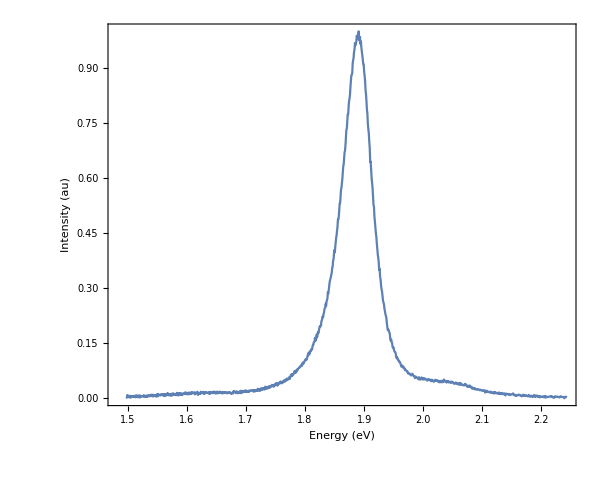

```mathematica
ListLinePlot[evSpot23,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
fit23=Interpolation[evSpot23,InterpolationOrder->1];
fit24=Interpolation[evSpot24,InterpolationOrder->1];
fit25=Interpolation[evSpot25,InterpolationOrder->1];
fit26=Interpolation[evSpot26,InterpolationOrder->1];
```

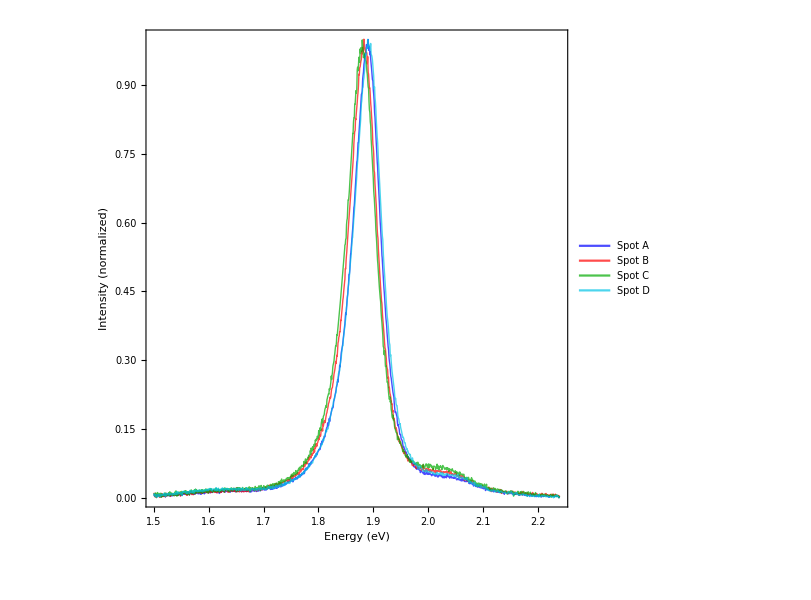

```mathematica
Plot[{fit23[x],fit24[x],fit25[x],fit26[x]},{x,1.5,2.24},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (normalized)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->{{Blue,Thick,Opacity[0.7]},{Red,Thick,Opacity[0.7]},{Darker[Green],Thick,Opacity[0.7]},{RGBColor[0.,0.77,0.9], Thick, Opacity[0.7]}},PlotLegends->Placed[{"Spot A","Spot B","Spot C", "Spot D"},{Right,Top}]]
```

```mathematica
FindMaximum[fit23[x],{x,1.9,2.2}]
```

{1.,{x→1.89063}}

```mathematica
FindMaximum[fit24[x],{x,1.9,2.1}]
```

{1.,{x→1.88291}}

```mathematica
FindMaximum[fit25[x],{x,1.9,2.1}]
```

{1.,{x→1.87984}}

```mathematica
FindMaximum[fit23[x],{x,1.9,2.1}]
```

{0.984499,{x→1.88908}}

```mathematica
monolayer=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/mono13.csv","CSV"];
```

```mathematica
overlap=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/overlap5.csv","CSV"];
```

```mathematica
rescaledMonolayer=Rescale[monolayer⟦2;;-1,2⟧];
rescaledOverlap=Rescale[overlap⟦2;;-1,2⟧];
```

```mathematica
evMonolayer=Table[{1239.8/monolayer⟦i+1,1⟧,monolayer⟦i+1,2⟧},{i,Length@monolayer-1}];
```

```mathematica
evOverlap=Table[{1239.8/overlap⟦i+1,1⟧,rescaledOverlap⟦i⟧},{i,Length@overlap-1}];
```

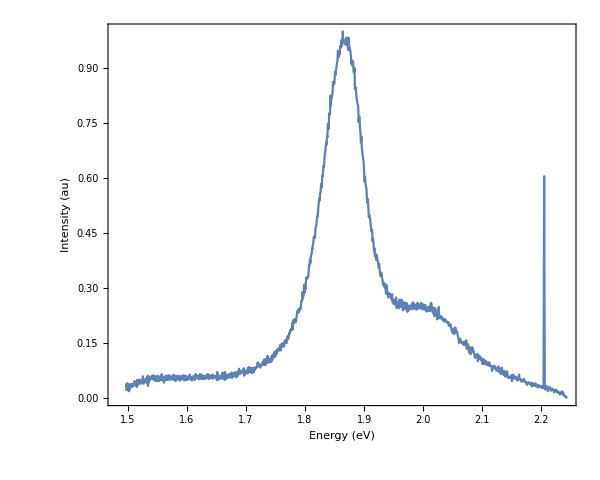

```mathematica
ListLinePlot[evMonolayer,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
Length@monolayer
```

1025

```mathematica
rescaledMonolayer⟦37⟧
```

0.605263

```mathematica
evMonolayer = Delete[evMonolayer,37];
```

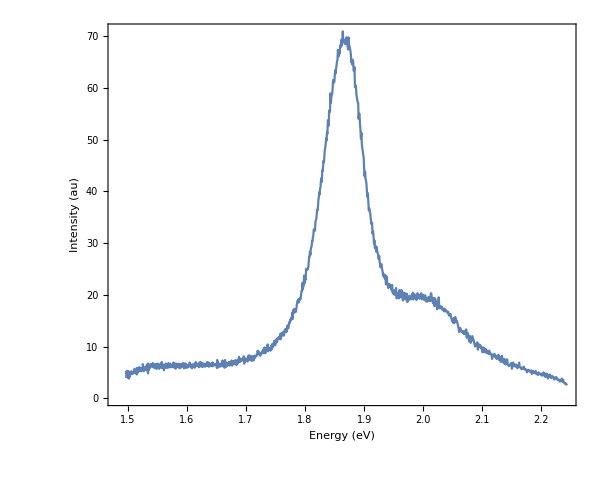

```mathematica
ListLinePlot[evMonolayer,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

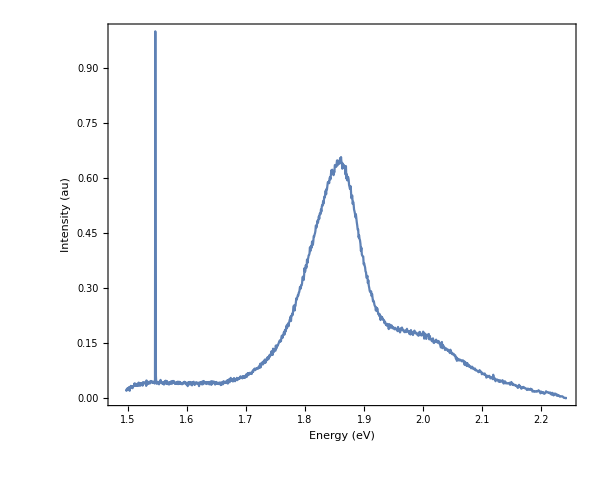

```mathematica
ListLinePlot[evOverlap,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
overlap=Delete[overlap,926];
```

```mathematica
rescaledOverlap=Rescale[overlap⟦2;;-1,2⟧];
```

```mathematica
evOverlap=Table[{1239.8/overlap⟦i+1,1⟧,overlap⟦i+1,2⟧},{i,Length@overlap-1}];
```

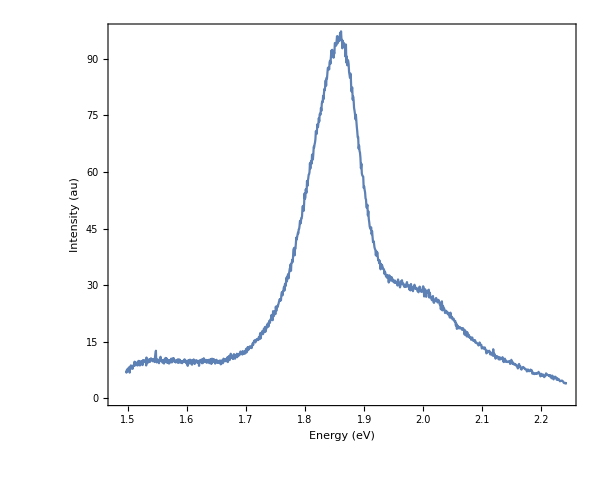

```mathematica
ListLinePlot[evOverlap,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```

```mathematica
fitMonolayer=Interpolation[evMonolayer,InterpolationOrder->1];
fitOverlap=Interpolation[evOverlap,InterpolationOrder->1];
```

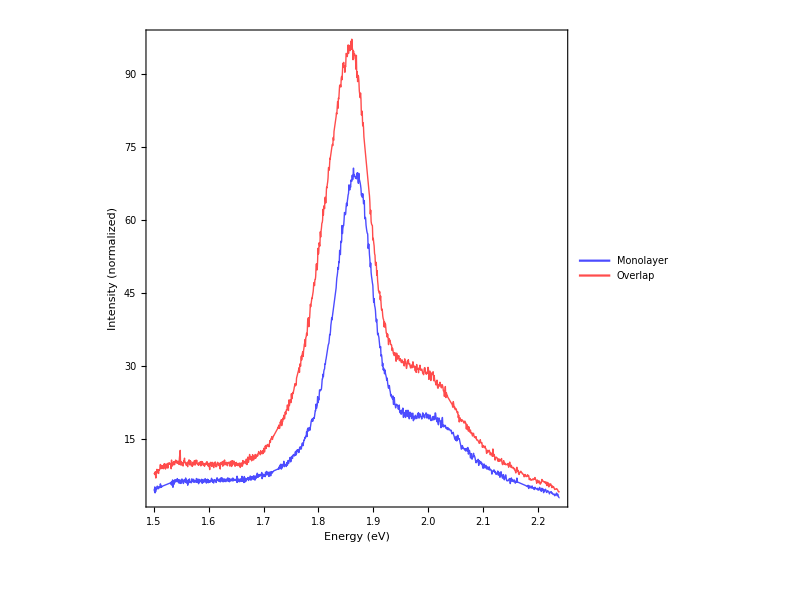

```mathematica
Plot[{fitMonolayer[x],fitOverlap[x]},{x,1.5,2.24},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (normalized)"},LabelStyle->{Black,20},ImageSize->600,AspectRatio->1,FrameTicks->{Automatic,None},PlotStyle->{{Blue,Thick,Opacity[0.7]},{Red,Thick,Opacity[0.7]}},PlotLegends->Placed[{"Monolayer","Overlap"},{Right,Top}]]
```

```mathematica
monolayer2=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/mono11.csv","CSV"];
overlap2=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Dissertation/Figures/overlap0.csv","CSV"];
```

```mathematica
evMonolayer2=Table[{1239.8/monolayer2⟦i+1,1⟧,monolayer2⟦i+1,2⟧},{i,Length@monolayer2-1}];
```

```mathematica
evOverlap2=Table[{1239.8/overlap2⟦i+1,1⟧,overlap2⟦i+1,2⟧},{i,Length@overlap2-1}];
```

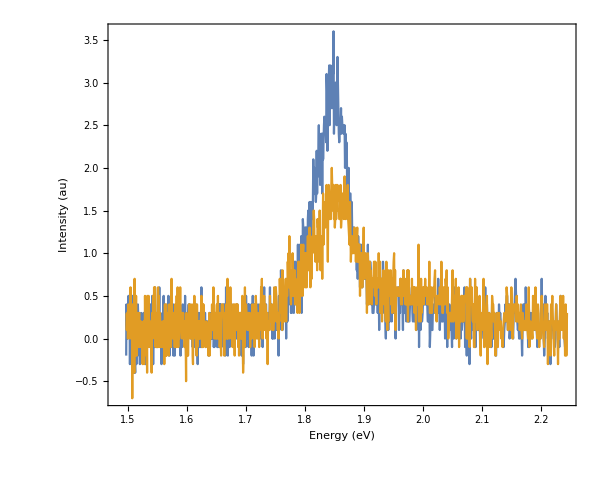

```mathematica
ListLinePlot[{evMonolayer2, evOverlap2},PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Intensity (au)"},LabelStyle->{Black,18},ImageSize->600,AspectRatio->0.8]
```